# Fix Wrapping

```mathematica
FixWrapping[datainput_,signinput_]:=Module[
{data=datainput,data2,t,fix,div,lm,ignoreme,x,i,sign},
Which[signinput=="+",sign=1,signinput=="-",sign=-1];
FixWrapMakeMonotonic[data,sign];
];
(* This function was developed to account for wrapping in faraday rotation data. *)
FixWrapMakeMonotonic[ordPair_,posOrNegSlope_]:=Module[
{grouped,posDetuningSorted,negDetuningSorted,
t,data,i,sign,mod,fixedData},
t=Transpose[ordPair];
(* Put the data in the form 1/detuning vs. rotation angle, so the variables should be linearly related *)
data=Transpose[{1/t[[1]],t[[2]]}];
(* 
 * We know that when pumping with S+ light, there should be a negative slope, 
 * negative detunings should have a positive rotation and positive detunings 
* should have a negative rotation. The opposite is true for S- light. The
* next bit of code adds wrapping amounts until this condition is satisfied.
*)
For[i=1,i≤Length[data],i++,
(* If the data point is not in the right quadrant *)
If[data[[i]][[1]]*data[[i]][[2]]*posOrNegSlope <0,
(* For negative slopes (positive slopes),
 * If the detuning is negative (positive),
 * numbers must be added (subtracted) 
* to move the data point to the correct quadrant. 
* The detuning being the opposite means
* the opposite operation is needed
 *)
If[data[[i]][[1]]*posOrNegSlope>0,mod=1,mod=-1];
(* Make the corresponding modification *)
data[[i]][[2]]=data[[i]][[2]]+mod*π/2;
];
];
(*
 * But it's still possible more modification is needed to the dataset.
* The next piece of code ensures that the rotation amount increases 
* as we move to smaller detunings by adding wrapping amounts until 
* smaller detunings have larger rotation angles. 
*)
(* I start by separating into positive and negative detunings *)
grouped=GroupBy[data,Positive[#1[[1]]]&];
(* Then sort them so that we start at large detunings and work
* towards smaller ones. *)
posDetuningSorted=Sort[grouped[True],Abs[#1[[1]]]<Abs[#2[[1]]]&];
negDetuningSorted=Sort[grouped[False],Abs[#1[[1]]]<Abs[#2[[1]]]&];
(* This function adds the wrapping. The second argument should
* be 1 if rotation is more positive as detuning decreases. It should
* be -1 if rotation is more negative as detuning decreases.
*)
posDetuningSorted=AddWrap[posDetuningSorted,posOrNegSlope];
negDetuningSorted=AddWrap[negDetuningSorted,posOrNegSlope*-1];
(* Package everything together and ship it out in the original format *)
fixedData=Join[posDetuningSorted,negDetuningSorted];
t=Transpose[fixedData];
fixedData=Transpose[{1/t[[1]],t[[2]]}];
fixedData=Sort[fixedData,#1[[1]]<#2[[1]]&]
];

(* This is a helper function for Fixing the rotation. It makes sure that the
* amount of rotation always increases with decreasing detuning.
*)
Clear[AddWrap];
AddWrap[sortedDataset_List,modifier_]:=Module[
{i,next,tol ,workingDataset=sortedDataset},
For[i=1,i<Length[workingDataset],i++,
next=i+1;
(* Check that the smaller detuning is a larger value, withing some tolerance.*)
tol=1.1;(*tolerance is 10 percent *)
While[Abs[workingDataset[[i,2]]]>Abs[workingDataset[[next,2]]]*tol,
workingDataset[[next,2]]+=(modifier*π/2);
];
];
workingDataset
];
```

```mathematica
FixWrappingOld1[datainput_,signinput_]:=Module[
{data,data2,t,fix,div,lm,ignoreme,x,i,sign},
data=datainput;
t=Transpose[data];
data=Transpose[{1/t[[1]],t[[2]]}];
lm=LinearModelFit[data,x,x];
lm["RSquared"];
Which[signinput=="+",sign=1,signinput=="-",sign=-1];
data2={{data[[1,1]],data[[1,2]]},{data[[8,1]],data[[8,2]]}};
Which[(data2[[1,2]]*sign)>0,data2[[1,2]]=(data2[[1,2]]-((π/2)*sign)),(data2[[1,2]]*sign)<0,ignoreme=0];
Which[(data2[[2,2]]*sign)<0,data2[[2,2]]=(data2[[2,2]]+((π/2)*sign)),(data2[[2,2]]*sign)>0,ignoreme=0];
data[[1,2]]=data2[[1,2]];
data[[8,2]]=data2[[2,2]];
data2={{data[[2,1]],data[[2,2]]},{data[[1,1]],data[[1,2]]},{data[[8,1]],data[[8,2]]}};
lm=LinearModelFit[data2,x,x];
For[i=0,i<5,i++,
div=i*sign*(π/2);
data2[[1,2]]=data2[[1,2]]-div;
lm=LinearModelFit[data2,x,x];
Which[lm["RSquared"]>.99,fix=div,lm["RSquared"]<.99,ignoreme=0];
data2[[1,2]]=data2[[1,2]]+div;];
data2[[1,2]]=data2[[1,2]]-fix;
data[[2,2]]=data2[[1,2]];
data2={{data[[2,1]],data[[2,2]]},{data[[1,1]],data[[1,2]]},{data[[8,1]],data[[8,2]]},{data[[7,1]],data[[7,2]]}};
lm=LinearModelFit[data2,x,x];
For[i=0,i<5,i++,
div=i*sign*(π/2);
data2[[4,2]]=data2[[4,2]]+div;
lm=LinearModelFit[data2,x,x];
Which[lm["RSquared"]>.99,fix=div,lm["RSquared"]<.99,ignoreme=0];
data2[[4,2]]=data2[[4,2]]-div;];
data2[[4,2]]=data2[[4,2]]+fix;
data[[7,2]]=data2[[4,2]];
data2={{data[[3,1]],data[[3,2]]},{data[[2,1]],data[[2,2]]},{data[[1,1]],data[[1,2]]},{data[[8,1]],data[[8,2]]},{data[[7,1]],data[[7,2]]}};
lm=LinearModelFit[data2,x,x];
For[i=0,i<5,i++,
div=i*sign*(π/2);
data2[[1,2]]=data2[[1,2]]-div;
lm=LinearModelFit[data2,x,x];
Which[lm["RSquared"]>.99,fix=div,lm["RSquared"]<.99,ignoreme=0];
data2[[1,2]]=data2[[1,2]]+div;];
data2[[1,2]]=data2[[1,2]]-fix;
data[[3,2]]=data2[[1,2]];
data2={{data[[3,1]],data[[3,2]]},{data[[2,1]],data[[2,2]]},{data[[1,1]],data[[1,2]]},{data[[8,1]],data[[8,2]]},{data[[7,1]],data[[7,2]]},{data[[6,1]],data[[6,2]]}};
lm=LinearModelFit[data2,x,x];
For[i=0,i<5,i++,
div=i*sign*(π/2);
data2[[6,2]]=data2[[6,2]]+div;
lm=LinearModelFit[data2,x,x];
Which[lm["RSquared"]>.99,fix=div,lm["RSquared"]<.99,ignoreme=0];
data2[[6,2]]=data2[[6,2]]-div;];
data2[[6,2]]=data2[[6,2]]+fix;
data[[6,2]]=data2[[6,2]];
data2={{data[[4,1]],data[[4,2]]},{data[[3,1]],data[[3,2]]},{data[[2,1]],data[[2,2]]},{data[[1,1]],data[[1,2]]},{data[[8,1]],data[[8,2]]},{data[[7,1]],data[[7,2]]},{data[[6,1]],data[[6,2]]}};
lm=LinearModelFit[data2,x,x];
For[i=0,i<5,i++,
div=i*sign*(π/2);
data2[[1,2]]=data2[[1,2]]-div;
lm=LinearModelFit[data2,x,x];
Which[lm["RSquared"]>.99,fix=div,lm["RSquared"]<.99,ignoreme=0];
data2[[1,2]]=data2[[1,2]]+div;];
data2[[1,2]]=data2[[1,2]]-fix;
data[[4,2]]=data2[[1,2]];
data2={{data[[4,1]],data[[4,2]]},{data[[3,1]],data[[3,2]]},{data[[2,1]],data[[2,2]]},{data[[1,1]],data[[1,2]]},{data[[8,1]],data[[8,2]]},{data[[7,1]],data[[7,2]]},{data[[6,1]],data[[6,2]]},{data[[5,1]],data[[5,2]]}};
lm=LinearModelFit[data2,x,x];
For[i=0,i<5,i++,
div=i*sign*(π/2);
data2[[8,2]]=data2[[8,2]]+div;
lm=LinearModelFit[data2,x,x];
Which[lm["RSquared"]>.99,fix=div,lm["RSquared"]<.99,ignoreme=0];
data2[[8,2]]=data2[[8,2]]-div;];
data2[[8,2]]=data2[[8,2]]+fix;
data[[5,2]]=data2[[8,2]];
data=Transpose[{1/Transpose[data][[1]],Transpose[data][[2]]}]
];
```

```mathematica
1
```

1

{{-0.0344199,-0.753146},{0.0303242,0.577507}}

FittedModel[-0.0457312+20.5525 x]

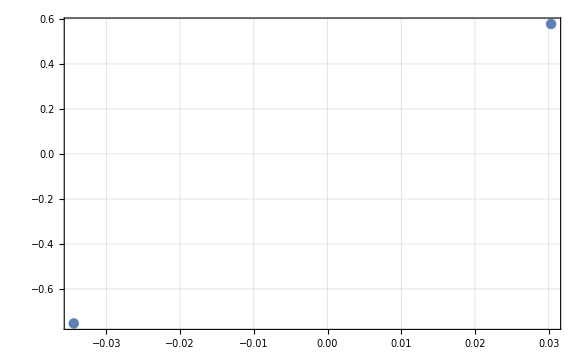

```mathematica
data2={{data[[1,1]],data[[1,2]]},{data[[8,1]],data[[8,2]]}}
lm=LinearModelFit[data2,x,x]
ListPlot[data2]
```

```mathematica
Which[(data2[[1,2]]*sign)>0,data2[[1,2]]=(data2[[1,2]]-((π/2)*sign)),(data2[[1,2]]*sign)<0,ignoreme=0]
Which[(data2[[2,2]]*sign)<0,data2[[2,2]]=(data2[[2,2]]+((π/2)*sign)),(data2[[2,2]]*sign)>0,ignoreme=0]
data[[1,2]]=data2[[1,2]]
data[[8,2]]=data2[[2,2]]
data
ListPlot[data2]
```

0

0

-0.753146

0.577507

{{-0.0344199,-0.753146},{-0.0383391,-0.836309},{-0.0527343,-1.18063},{-0.0557631,-1.23169},{0.0500576,0.959098},{0.0477395,0.967633},{0.0333923,0.650337},{0.0303242,0.577507}}

-Graphics-

{{-0.0383391,-0.836309},{-0.0344199,-0.753146},{0.0303242,0.577507}}

FittedModel[-0.0463011+20.5738 x]

-0.836309

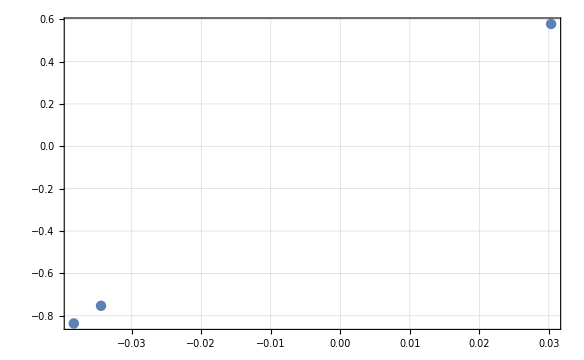

-0.836309

```mathematica
data2={{data[[2,1]],data[[2,2]]},{data[[1,1]],data[[1,2]]},{data[[8,1]],data[[8,2]]}}
lm=LinearModelFit[data2,x,x]
For[i=0,i<5,i++,
div=i*sign*(π/2);
data2[[1,2]]=data2[[1,2]]-div;
lm=LinearModelFit[data2,x,x];
Which[lm["RSquared"]>.99,fix=div,lm["RSquared"]<.99,ignoreme=0];
data2[[1,2]]=data2[[1,2]]+div;]
data2[[1,2]]=data2[[1,2]]-fix
ListPlot[data2]
data[[2,2]]=data2[[1,2]]
```

{{-0.0383391,-0.836309},{-0.0344199,-0.753146},{0.0303242,0.577507},{0.0333923,0.650337}}

FittedModel[-0.0437268+20.6473 x]

0.650337

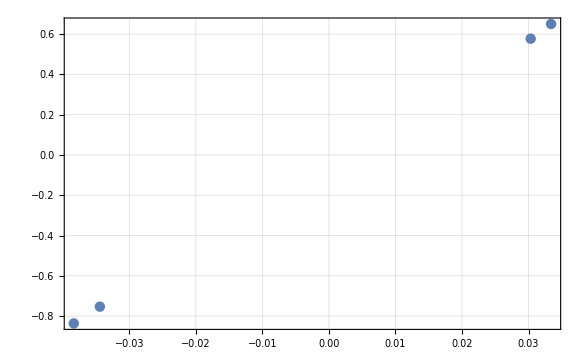

0.650337

```mathematica
data2={{data[[2,1]],data[[2,2]]},{data[[1,1]],data[[1,2]]},{data[[8,1]],data[[8,2]]},{data[[7,1]],data[[7,2]]}}
lm=LinearModelFit[data2,x,x]
For[i=0,i<5,i++,
div=i*sign*(π/2);
data2[[4,2]]=data2[[4,2]]+div;
lm=LinearModelFit[data2,x,x];
Which[lm["RSquared"]>.99,fix=div,lm["RSquared"]<.99,ignoreme=0];
data2[[4,2]]=data2[[4,2]]-div;]
data2[[4,2]]=data2[[4,2]]+fix
ListPlot[data2]
data[[7,2]]=data2[[4,2]]
```

{{-0.0527343,-1.18063},{-0.0383391,-0.836309},{-0.0344199,-0.753146},{0.0303242,0.577507},{0.0333923,0.650337}}

FittedModel[-0.0497671+20.9368 x]

-1.18063

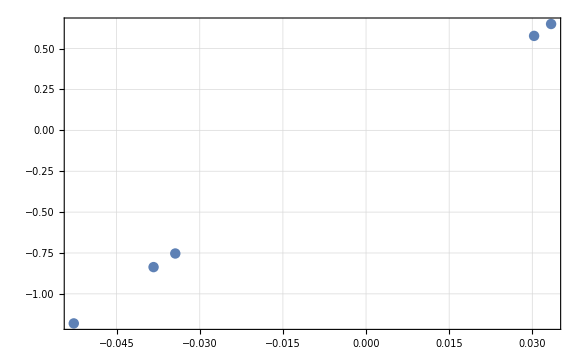

-1.18063

```mathematica
data2={{data[[3,1]],data[[3,2]]},{data[[2,1]],data[[2,2]]},{data[[1,1]],data[[1,2]]},{data[[8,1]],data[[8,2]]},{data[[7,1]],data[[7,2]]}}
lm=LinearModelFit[data2,x,x]
For[i=0,i<5,i++,
div=i*sign*(π/2);
data2[[1,2]]=data2[[1,2]]-div;
lm=LinearModelFit[data2,x,x];
Which[lm["RSquared"]>.99,fix=div,lm["RSquared"]<.99,ignoreme=0];
data2[[1,2]]=data2[[1,2]]+div;]
data2[[1,2]]=data2[[1,2]]-fix
ListPlot[data2]
data[[3,2]]=data2[[1,2]]
```

{{-0.0527343,-1.18063},{-0.0383391,-0.836309},{-0.0344199,-0.753146},{0.0303242,0.577507},{0.0333923,0.650337},{0.0477395,0.967633}}

FittedModel[-0.0465706+21.029 x]

0.967633

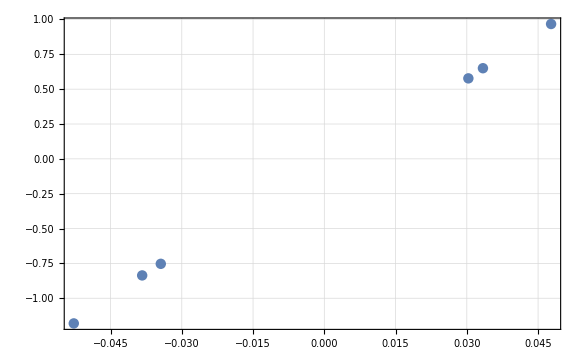

0.967633

```mathematica
data2={{data[[3,1]],data[[3,2]]},{data[[2,1]],data[[2,2]]},{data[[1,1]],data[[1,2]]},{data[[8,1]],data[[8,2]]},{data[[7,1]],data[[7,2]]},{data[[6,1]],data[[6,2]]}}
lm=LinearModelFit[data2,x,x]
For[i=0,i<5,i++,
div=i*sign*(π/2);
data2[[6,2]]=data2[[6,2]]+div;
lm=LinearModelFit[data2,x,x];
Which[lm["RSquared"]>.99,fix=div,lm["RSquared"]<.99,ignoreme=0];
data2[[6,2]]=data2[[6,2]]-div;]
data2[[6,2]]=data2[[6,2]]+fix
ListPlot[data2]
data[[6,2]]=data2[[6,2]]
```

{{-0.0557631,-1.23169},{-0.0527343,-1.18063},{-0.0383391,-0.836309},{-0.0344199,-0.753146},{0.0303242,0.577507},{0.0333923,0.650337},{0.0477395,0.967633}}

FittedModel[-0.0478844+21.076 x]

-1.23169

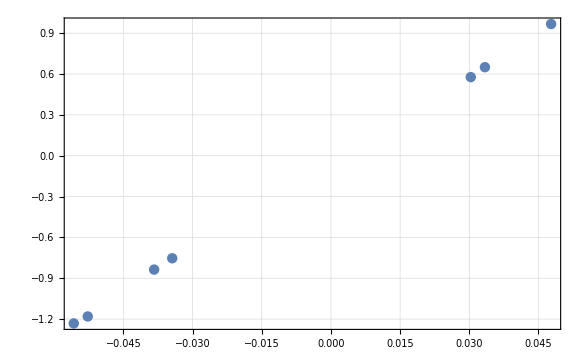

-1.23169

```mathematica
data2={{data[[4,1]],data[[4,2]]},{data[[3,1]],data[[3,2]]},{data[[2,1]],data[[2,2]]},{data[[1,1]],data[[1,2]]},{data[[8,1]],data[[8,2]]},{data[[7,1]],data[[7,2]]},{data[[6,1]],data[[6,2]]}}
lm=LinearModelFit[data2,x,x]
For[i=0,i<5,i++,
div=i*sign*(π/2);
data2[[1,2]]=data2[[1,2]]-div;
lm=LinearModelFit[data2,x,x];
Which[lm["RSquared"]>.99,fix=div,lm["RSquared"]<.99,ignoreme=0];
data2[[1,2]]=data2[[1,2]]+div;]
data2[[1,2]]=data2[[1,2]]-fix
ListPlot[data2]
data[[4,2]]=data2[[1,2]]
```

{{-0.0557631,-1.23169},{-0.0527343,-1.18063},{-0.0383391,-0.836309},{-0.0344199,-0.753146},{0.0303242,0.577507},{0.0333923,0.650337},{0.0477395,0.967633},{0.0500576,0.959098}}

FittedModel[-0.0542947+20.9113 x]

0.959098

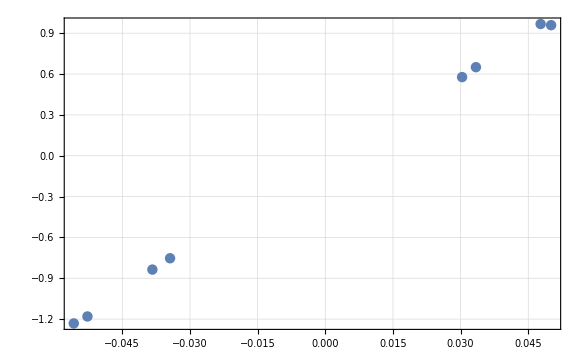

0.959098

```mathematica
data2={{data[[4,1]],data[[4,2]]},{data[[3,1]],data[[3,2]]},{data[[2,1]],data[[2,2]]},{data[[1,1]],data[[1,2]]},{data[[8,1]],data[[8,2]]},{data[[7,1]],data[[7,2]]},{data[[6,1]],data[[6,2]]},{data[[5,1]],data[[5,2]]}}
lm=LinearModelFit[data2,x,x]
For[i=0,i<5,i++,
div=i*sign*(π/2);
data2[[8,2]]=data2[[8,2]]+div;
lm=LinearModelFit[data2,x,x];
Which[lm["RSquared"]>.99,fix=div,lm["RSquared"]<.99,ignoreme=0];
data2[[8,2]]=data2[[8,2]]-div;]
data2[[8,2]]=data2[[8,2]]+fix
ListPlot[data2]
data[[5,2]]=data2[[8,2]]
```

```mathematica
t=Transpose[data]
data=Transpose[{1/t[[1]],t[[2]]}]
```

{{-0.0344199,-0.0383391,-0.0527343,-0.0557631,0.0500576,0.0477395,0.0333923,0.0303242},{-0.753146,-0.836309,-1.18063,-1.23169,0.959098,0.967633,0.650337,0.577507}}

{{-29.053,-0.753146},{-26.083,-0.836309},{-18.963,-1.18063},{-17.933,-1.23169},{19.977,0.959098},{20.947,0.967633},{29.947,0.650337},{32.977,0.577507}}